```mathematica
Get["http://www.fmt.if.usp.br/~gtlandi/download/melt.m"](*Requires Internet Connection*)
```

```mathematica
LoadPauliMatrices[]
```

Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, GMAT[θ,ϕ]

## Landau-Zener model (Recreating the figures in https://arxiv.org/abs/2109.10145 )

### Fig 1

```mathematica
Δ = 1.;
g0 = -10Δ;
g[t_]:= g0 - 2g0(t/tf);
HLZ[t_]:= Δ σx+g[t]σz;
```

```mathematica
divs = 1000;(*Number of time steps*)
tf = 2;
dt = tf/divs;
HN = Table[HLZ[i dt],{i,0,divs}];
```

```mathematica
evals = Eigvals/@HN;(*Eigenvalues at each time step*)
gaps = evals[[;;,2]]-evals[[;;,1]];(*Subtract all the ground state energies from the excited state energies*)
```

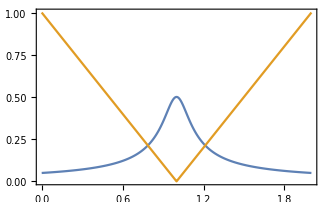

```mathematica
ListPlot[{Table[{i dt,1/gaps[[i+1]]},{i,0,divs}],Table[{i dt,Abs[g[i dt]/g0]},{i,0,divs}]},Joined->True](*Fig 1(a)*)
```

```mathematica
μ = 1/2 √((√(τQ^4 Δ^4+4 g0^2 τQ^2)-τQ^2 Δ^2)/(2g0^2));(*Taken directly from the paper*)
```

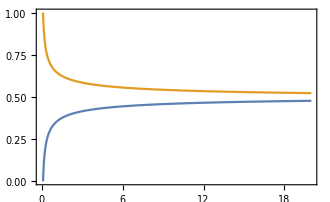

```mathematica
Plot[{(τQ/2 - μ)/τQ,(τQ/2 + μ)/τQ},{τQ,0,20},PlotRange->{0,1}](*Fig 1(b)*)
```

### Fig 2

```mathematica
f[x_]:= 1/(1+ⅇ^(-m x));
S[x_] := f[x-tm]*f[tp-x];(*This function gives a smooth turning on of the counter-diabatic Hamiltonian*)
```

```mathematica
divs = 1000;(*This can be increased for higher precision*)
tf = 25.;(*You can change tf to get the different subplots*)
dt = tf/divs;
{HN,HCD} = CounterDiabaticHamiltonian[HLZ,tf,dt];
groundStates = (Eigvecs/@HN)[[;;,1]];
adi = Quiet@UnitaryDynamics[HN,dt,tf,groundStates[[1]]][[;;,2]];
full = Quiet@UnitaryDynamics[HN+HCD,dt,tf,groundStates[[1]]][[;;,2]];
m = 400/Δ;
tp = tf/2 + (μ/. τQ -> tf);
tm = tf/2 - (μ/. τQ -> tf);
Slist = Quiet@Table[S[i dt],{i,0,divs}];
partial = Quiet@UnitaryDynamics[HN+Slist*HCD,dt,tf,groundStates[[1]]][[;;,2]];
```

```mathematica
adiF = Abs[MapThread[Dot,{groundStates,adi}]]^2;(*This can also be done with tables but MapThread is more efficient*)
fullF = Abs[MapThread[Dot,{groundStates,full}]]^2;
partialF = Abs[MapThread[Dot,{groundStates,partial}]]^2;
```

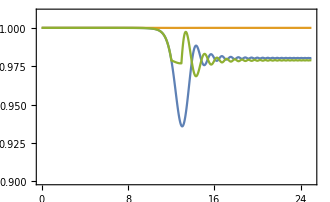

```mathematica
ListPlot[{Table[{i dt,adiF[[i+1]]},{i,0,divs}],Table[{i dt,fullF[[i+1]]},{i,0,divs}],Table[{i dt,partialF[[i+1]]},{i,0,divs}]},Joined->True,PlotRange->{0.9,1.01}](*Fig 2*)
```

### Fig 3(a)

```mathematica
tlist = linspace[0.01,25,100];
do[
divs = 1000;
dt = tf/divs;
{HN,HCD} = Quiet@CounterDiabaticHamiltonian[HLZ,tf,dt];
groundStates = (Eigvecs/@HN)[[;;,1]];
adi = Quiet@UnitaryDynamics[HN,dt,tf,groundStates[[1]],True];
m = 400/Δ;
tp = tf/2 + (μ/. τQ -> tf);
tm = tf/2 - (μ/. τQ -> tf);
Slist = Quiet@Table[S[i dt],{i,0,divs}];
partial = Quiet@UnitaryDynamics[HN+Slist*HCD,dt,tf,groundStates[[1]],True](*We only care about the final states*);
aF[tf] = Abs[Dot[groundStates[[-1]],adi]]^2;
pF[tf] = Abs[Dot[groundStates[[-1]],partial]]^2;
,
{tf,tlist}]
```

0h : 0m : 15s

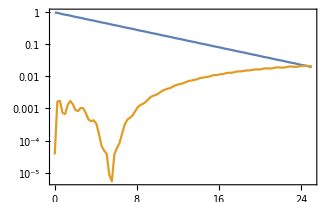

```mathematica
ListLogPlot[{Table[{i ,1-aF[i]},{i,tlist}],Table[{i ,1-pF[i]},{i,tlist}]},Joined->True](*Fig 3(a)*)
```

### Fig 3(b)

```mathematica
tlist = linspace[0.1,25,100];(*Starting at 0 would throw up errors*)
Quiet@do[
divs = 1000;
dt = tf/divs;
{HN,HCD} = CounterDiabaticHamiltonian[HLZ,tf,dt];
m = 400/Δ;
tp = tf/2 + (μ/. τQ -> tf);
tm = tf/2 - (μ/. τQ -> tf);
Slist = Table[S[i dt],{i,0,divs}];
norm = Sqrt/@Tr/@MapThread[Dot,{ConjugateTranspose/@HCD,HCD}]//Chop(*Cost for full driving at each time step*);
normP = Sqrt/@Tr/@MapThread[Dot,{ConjugateTranspose/@(Slist*HCD),Slist*HCD}]//Chop(*Cost for partial driving at each time step*);
cost[tf] = Trapz[norm,dt]/tf(*Integrate for average cost*);
costP[tf] = Trapz[normP,dt]/tf;
,
{tf,tlist}]
```

0h : 0m : 10s

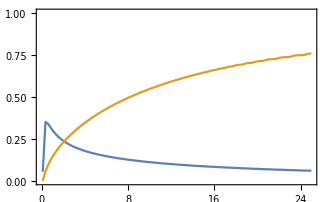

```mathematica
ListPlot[{Table[{i ,cost[i]-costP[i]},{i,tlist}],Table[{i ,1-costP[i]/cost[i]},{i,tlist}]},Joined->True,PlotRange->{0,1}](*Fig 3(b)*)
```